```mathematica
uptvnewvold[Z_,N_,dddt_,c_]:=
(pt=Z[[1]];
pvnew=Z[[2]];
pvold=Z[[3]];
pv=Z[[4]];
nt=pt+dddt;
vhat=Fourier[pv,FourierParameters->{1,-1}];
what=I*Join[Range[0,N/2-1],{0},Range[-N/2+1,-1]]*vhat;
w=Re[InverseFourier[what,FourierParameters->{1,-1}]];
nvnew=pvold-2*dddt*c*w;
nvold=pv;
nv=nvnew;
{nt,nvnew,nvold,nv})
```

```mathematica
(NN=128;
h=2*Pi/NN;
x=h*Range[1,NN];
t=0;
ddt=h/4;
c=0.2+Sin[x-1]^2;
v=Exp[-100*(x-1)^2];
vold=Exp[-100*(x-0.2*ddt-1)^2];
tmax=8;
tplot=0.15;
nplots=Round[tmax/tplot];
plotgap=Round[tplot/ddt];
dt=tplot/plotgap;
mydata=NestList[
Nest[
uptvnewvold[#,NN,ddt,c]&,
#,plotgap]&,
{t,{},vold,v},nplots];
ListPlot3D[Flatten[Table[MapIndexed[{First[#2],mydata[[tt,1]],#1}&,mydata[[tt,4]]],{tt,1,Length[mydata]}],1],PlotRange->All])
```

-Graphics3D-

```mathematica
NN=128;
h=2*Pi/NN;
x=h*Range[1,NN];
t=0;
ddt=h/4;
c=0.2+Sin[x-1]^2;
v=Exp[-100*(x-1)^2];
vold=Exp[-100*(x-0.2*ddt-1)^2];
tmax=8;
tplot=0.15;
nplots=Round[tmax/tplot];
plotgap=Round[tplot/ddt];
dt=tplot/plotgap;
```

```mathematica
D[Exp[-100*(xx-1)^2],xx]
```

-200 ⅇ^(-100 (-1+xx)^2) (-1+xx)

```mathematica
vold2=v+ddt*c*(-200 ⅇ^(-100 (-1+x)^2) (-1+x))
```

{1.61652×10^-39,1.34034×10^-35,6.84959×10^-32,2.15844×10^-28,4.19651×10^-25,5.03734×10^-22,3.73599×10^-19,1.71343×10^-16,4.86371×10^-14,8.55277×10^-12,9.32536×10^-10,6.30937×10^-8,2.65057×10^-6,0.000069167,0.00112127,0.0112898,0.0705636,0.27354,0.656903,0.975915,0.895471,0.506574,0.176332,0.037685,0.00493263,0.00039426,0.0000191726,5.64453×10^-7,9.98891×10^-9,1.0506×10^-10,6.43656×10^-13,2.20218×10^-15,3.73803×10^-18,1.47088×10^-21,-4.67127×10^-24,-7.83405×10^-27,-5.39872×10^-30,-1.98429×10^-33,-4.16837×10^-37,-5.15058×10^-41,-3.79902×10^-45,-1.68705×10^-49,-4.53499×10^-54,-7.40621×10^-59,-7.36713×10^-64,-4.47189×10^-69,-1.65876×10^-74,-3.76387×10^-80,-5.22885×10^-86,-4.45023×10^-92,-2.3216×10^-98,-7.4267×10^-105,-1.45731×10^-111,-1.75453×10^-118,-1.29631×10^-125,-5.87838×10^-133,-1.63624×10^-140,-2.79577×10^-148,-2.93243×10^-156,-1.88806×10^-164,-7.46172×10^-173,-1.80992×10^-181,-2.69413×10^-190,-2.46062×10^-199,-1.37863×10^-208,-4.73714×10^-218,-9.97993×10^-228,-1.28864×10^-237,-1.01944×10^-247,-4.93895×10^-258,-1.46467×10^-268,-2.65745×10^-279,-2.94842×10^-290,-1.9995×10^-301,-8.28553944392315×10^-313,-2.09791050146871×10^-324,-3.24764402418415×10^-336,-3.07873510020235×10^-348,-1.79344461352884×10^-360,-6.4602733181052×10^-373,-1.45401549507754×10^-385,-2.07575641087029×10^-398,-1.91386420928502×10^-411,-1.15770093573128×10^-424,-4.62263815561089×10^-438,-1.21003824391655×10^-451,-2.04337850108101×10^-465,-2.18646729641894×10^-479,-1.46076963343499×10^-493,-6.03247365706397×10^-508,-1.5305797173646×10^-522,-2.37819904187233×10^-537,-2.25951110150509×10^-552,-1.3120153470826×10^-567,-4.65639216796264×10^-583,-1.01041682542899×10^-598,-1.34123355961342×10^-614,-1.08966660662949×10^-630,-5.42125944569058×10^-647,-1.65251187945563×10^-663,-3.08766999885977×10^-680,-3.53789307952548×10^-697,-2.48687039352006×10^-714,-1.07276716740252×10^-731,-2.84075798644386×10^-749,-4.61909225769928×10^-767,-4.61291879396115×10^-785,-2.82997156599195×10^-803,-1.06672888643452×10^-821,-2.47092584935775×10^-840,-3.51768702415423×10^-859,-3.0781914017148×10^-878,-1.65582982174205×10^-897,-5.47583419798835×10^-917,-1.11333234026625×10^-936,-1.39173859652485×10^-956,-1.06969606751199×10^-976,-5.05519574649453×10^-997,-1.46888874910558×10^-1017,-2.6242504613042×10^-1038,-2.88252331593318×10^-1059,-1.94657370200827×10^-1080,-8.08113167093023×10^-1102,-2.06225845117543×10^-1123,-3.23476841718447×10^-1145,-3.11835376143382×10^-1167,-1.84729314197354×10^-1189,-6.72378850503641×10^-1212}

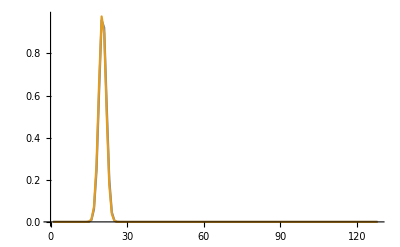

```mathematica
ListPlot[{vold,vold2},PlotRange->All,Joined->True]
```

```mathematica
uptvnewvold[Z_,N_,dddt_,c_]:=
(pt=Z[[1]];
pvnew=Z[[2]];
pvold=Z[[3]];
pv=Z[[4]];
nt=pt+dddt;
vhat=Fourier[pv,FourierParameters->{1,-1}];
what=I*Join[Range[0,N/2-1],{0},Range[-N/2+1,-1]]*vhat;
w=InverseFourier[what,FourierParameters->{1,-1}];
nvnew=pvold-2*dddt*c*w;
nvold=pv;
nv=nvnew;
{nt,nvnew,nvold,nv})
```

```mathematica
(NN=128;
h=2*Pi/NN;
x=h*Range[1,NN];
t=0;
ddt=h/4;
c=0.2+Sin[x-1]^2;
v=Exp[-100*(x-1)^2];
vold=v+ddt*c*(-200 ⅇ^(-100 (-1+x)^2) (-1+x));
tmax=8;
tplot=0.15;
nplots=Round[tmax/tplot];
plotgap=Round[tplot/ddt];
dt=tplot/plotgap;
mydata=NestList[
Nest[
uptvnewvold[#,NN,ddt,c]&,
#,plotgap]&,
{t,{},vold,v},nplots];
ListPlot3D[Flatten[Table[MapIndexed[{First[#2],mydata[[tt,1]],#1}&,mydata[[tt,4]]],{tt,1,Length[mydata]}],1],PlotRange->All])
```

-Graphics3D-

```mathematica
Plot[Integrate[Exp[-I*k*z]*Sin[z]/z,{z,-Infinity,Infinity}],{k,-5,5}]
```

$Aborted

```mathematica
Integrate[Exp[-I*0.5*z]*Sin[z]/z,{z,-Infinity,Infinity}]
```

3.14159+0. ⅈ

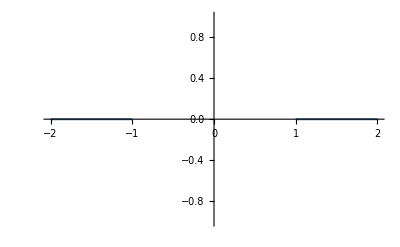

```mathematica
Plot[ConditionalExpression[0,Im[k]==0&&(Re[k]<-1||Re[k]>1)],{k,-2,2}]
```

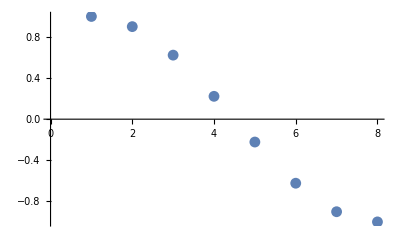

```mathematica
ListPlot[Table[Cos[Pi*j/7],{j,0,7}]]
```